## Load Data

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"HepLib.m"}]]
```

```mathematica
ResJ0=C2M@Import[FileNameJoin[{NotebookDirectory[],"J0.txt"}]];
ResJ1=C2M@Import[FileNameJoin[{NotebookDirectory[],"J1.txt"}]];
ResJ2=C2M@Import[FileNameJoin[{NotebookDirectory[],"J2.txt"}]];
```

-Graphics-

```mathematica
(*需要除以4，Subscript[对应上面的Φ, π]*)
ResJ0=ResJ0/4;
ResJ1=ResJ1/4;
ResJ2=ResJ2/4;
```

```mathematica
R0=Collect[Plus@@ResJ0,{C33,C66},Factor]
Variables[%]
```

(ⅈ C33 gs^6 S11 (2048 u^5 v^3-3072 u^5 v^2+1408 u^5 v-192 u^5-512 u^4 v^4-4096 u^4 v^3+5888 u^4 v^2-2240 u^4 v+256 u^4+2048 u^3 v^5-4096 u^3 v^4+8320 u^3 v^3-6848 u^3 v^2+1684 u^3 v-106 u^3-3072 u^2 v^5+5888 u^2 v^4-6848 u^2 v^3+4072 u^2 v^2-742 u^2 v+17 u^2+1408 u v^5-2240 u v^4+1684 u v^3-742 u v^2+114 u v-2 u-192 v^5+256 v^4-106 v^3+17 v^2-2 v))/(576 m^6 (u-1) u (2 u-1)^2 (v-1) v (2 v-1)^2 (4 u v-3 u-3 v+2) (4 u v-u-v))+(ⅈ C66 gs^6 S00 (2048 u^5 v^3-3072 u^5 v^2+1408 u^5 v-192 u^5-512 u^4 v^4-4096 u^4 v^3+5888 u^4 v^2-2240 u^4 v+256 u^4+2048 u^3 v^5-4096 u^3 v^4+8320 u^3 v^3-6848 u^3 v^2+1620 u^3 v-74 u^3-3072 u^2 v^5+5888 u^2 v^4-6848 u^2 v^3+4200 u^2 v^2-774 u^2 v+u^2+1408 u v^5-2240 u v^4+1620 u v^3-774 u v^2+146 u v-2 u-192 v^5+256 v^4-74 v^3+v^2-2 v))/(192 √6 m^6 (u-1) u (2 u-1)^2 (v-1) v (2 v-1)^2 (4 u v-3 u-3 v+2) (4 u v-u-v))

{C33,C66,gs,m,S00,S11,u,v}

```mathematica
Plus@@ResJ1//Simplify
Variables[%]
```

0

{}

```mathematica
R2=Plus@@ResJ2//Simplify
Variables[%]
```

-((ⅈ C33 gs^6 S11 (160 u^5 (32 v^3-48 v^2+22 v-3)-16 u^4 (32 v^4+736 v^3-1184 v^2+566 v-79)+2 u^3 (2560 v^5-5888 v^4+10400 v^3-10480 v^2+4478 v-599)+u^2 (-7680 v^5+18944 v^4-20960 v^3+13168 v^2-4282 v+485)+u (3520 v^5-9056 v^4+8956 v^3-4282 v^2+972 v-71)+v (-480 v^4+1264 v^3-1198 v^2+485 v-71)) (k.lim1001 (k-2 p).lim1002+p.lim1001 (p-2 k).lim1002+8 m^2 lim1002.lim1001))/(2304 √3 m^8 (1-2 u)^2 (u-1) u (1-2 v)^2 (v-1) v (u (4 v-3)-3 v+2) (u (4 v-1)-v)))

{C33,gs,m,S11,u,v,k.lim1001,lim1002.lim1001,(k-2 p).lim1002,p.lim1001,(p-2 k).lim1002}

## R0

```mathematica
RR0=-I R0/.{gs->√(απ 4),u->x,v->y};
```

### TEX

```mathematica
Factor@Coefficient[RR0,C33 S11]/.{1-x->X,x-1->-X,1-y->Y,y-1->-Y,4 x y-3x-3y+2->Expand[4 x y-3x-3y+2/.{x->1-X,y->1-Y}]}
```

(απ^3 (2048 x^5 y^3-3072 x^5 y^2+1408 x^5 y-192 x^5-512 x^4 y^4-4096 x^4 y^3+5888 x^4 y^2-2240 x^4 y+256 x^4+2048 x^3 y^5-4096 x^3 y^4+8320 x^3 y^3-6848 x^3 y^2+1684 x^3 y-106 x^3-3072 x^2 y^5+5888 x^2 y^4-6848 x^2 y^3+4072 x^2 y^2-742 x^2 y+17 x^2+1408 x y^5-2240 x y^4+1684 x y^3-742 x y^2+114 x y-2 x-192 y^5+256 y^4-106 y^3+17 y^2-2 y))/(9 m^6 x (2 x-1)^2 X y (2 y-1)^2 Y (4 x y-x-y) (4 X Y-X-Y))

```mathematica
Factor@Coefficient[RR0,C66 S00]/.{1-x->X,x-1->-X,1-y->Y,y-1->-Y,4 x y-3x-3y+2->Expand[4 x y-3x-3y+2/.{x->1-X,y->1-Y}]}
```

(απ^3 (2048 x^5 y^3-3072 x^5 y^2+1408 x^5 y-192 x^5-512 x^4 y^4-4096 x^4 y^3+5888 x^4 y^2-2240 x^4 y+256 x^4+2048 x^3 y^5-4096 x^3 y^4+8320 x^3 y^3-6848 x^3 y^2+1620 x^3 y-74 x^3-3072 x^2 y^5+5888 x^2 y^4-6848 x^2 y^3+4200 x^2 y^2-774 x^2 y+x^2+1408 x y^5-2240 x y^4+1620 x y^3-774 x y^2+146 x y-2 x-192 y^5+256 y^4-74 y^3+y^2-2 y))/(3 √6 m^6 x (2 x-1)^2 X y (2 y-1)^2 Y (4 x y-x-y) (4 X Y-X-Y))

### HepLib

```mathematica
Coefficient[RR0,C33 S11]/.{m->1,απ->1}
(4 u v-3 u-3 v+2)(4 u v-u-v) (2 u-1)^2(2 v-1)^2%//M2C;
(*Export[FileNameJoin[{NotebookDirectory[],"J033.txt"}],%]*)
```

(2048 x^5 y^3-3072 x^5 y^2+1408 x^5 y-192 x^5-512 x^4 y^4-4096 x^4 y^3+5888 x^4 y^2-2240 x^4 y+256 x^4+2048 x^3 y^5-4096 x^3 y^4+8320 x^3 y^3-6848 x^3 y^2+1684 x^3 y-106 x^3-3072 x^2 y^5+5888 x^2 y^4-6848 x^2 y^3+4072 x^2 y^2-742 x^2 y+17 x^2+1408 x y^5-2240 x y^4+1684 x y^3-742 x y^2+114 x y-2 x-192 y^5+256 y^4-106 y^3+17 y^2-2 y)/(9 (x-1) x (2 x-1)^2 (y-1) y (2 y-1)^2 (4 x y-3 x-3 y+2) (4 x y-x-y))

```mathematica
Coefficient[RR0,C66 S00]/.{m->1,απ->1}
(4 u v-3 u-3 v+2)(4 u v-u-v) (2 u-1)^2(2 v-1)^2%//M2C;
(*Export[FileNameJoin[{NotebookDirectory[],"J066.txt"}],%]*)
```

(2048 x^5 y^3-3072 x^5 y^2+1408 x^5 y-192 x^5-512 x^4 y^4-4096 x^4 y^3+5888 x^4 y^2-2240 x^4 y+256 x^4+2048 x^3 y^5-4096 x^3 y^4+8320 x^3 y^3-6848 x^3 y^2+1620 x^3 y-74 x^3-3072 x^2 y^5+5888 x^2 y^4-6848 x^2 y^3+4200 x^2 y^2-774 x^2 y+x^2+1408 x y^5-2240 x y^4+1620 x y^3-774 x y^2+146 x y-2 x-192 y^5+256 y^4-74 y^3+y^2-2 y)/(3 √6 (x-1) x (2 x-1)^2 (y-1) y (2 y-1)^2 (4 x y-3 x-3 y+2) (4 x y-x-y))

## R2

```mathematica
RR2=-I R2/.{gs->√(απ 4),u->x,v->y,(k-2 p).lim1002->3k.lim1002,(p-2 k).lim1002->-3k.lim1002,p.lim1001->-k.lim1001};
```

### TEX

```mathematica
Factor@Coefficient[RR2,C33 S11]/.{1-x->X,x-1->-X,1-y->Y,y-1->-Y,4 x y-3x-3y+2->Expand[4 x y-3x-3y+2/.{x->1-X,y->1-Y}]}
```

-((απ^3 (5120 x^5 y^3-7680 x^5 y^2+3520 x^5 y-480 x^5-512 x^4 y^4-11776 x^4 y^3+18944 x^4 y^2-9056 x^4 y+1264 x^4+5120 x^3 y^5-11776 x^3 y^4+20800 x^3 y^3-20960 x^3 y^2+8956 x^3 y-1198 x^3-7680 x^2 y^5+18944 x^2 y^4-20960 x^2 y^3+13168 x^2 y^2-4282 x^2 y+485 x^2+3520 x y^5-9056 x y^4+8956 x y^3-4282 x y^2+972 x y-71 x-480 y^5+1264 y^4-1198 y^3+485 y^2-71 y) (3 k.lim1001 k.lim1002+4 m^2 lim1002.lim1001))/(18 √3 m^8 x (2 x-1)^2 X y (2 y-1)^2 Y (4 x y-x-y) (4 X Y-X-Y)))

```mathematica
Factor@Coefficient[RR2,C66 S00]/.{1-x->X,x-1->-X,1-y->Y,y-1->-Y,4 x y-3x-3y+2->Expand[4 x y-3x-3y+2/.{x->1-X,y->1-Y}]}
```

0

### HepLib

```mathematica
Coefficient[RR2/(3 k.lim1001 k.lim1002+4 m^2 lim1002.lim1001)//Cancel,C33 S11]/.{m->1,απ->1}
(4 u v-3 u-3 v+2)(4 u v-u-v) (2 u-1)^2(2 v-1)^2%//M2C;
(*Export[FileNameJoin[{NotebookDirectory[],"J233.txt"}],%]*)
```

-((5120 x^5 y^3-7680 x^5 y^2+3520 x^5 y-480 x^5-512 x^4 y^4-11776 x^4 y^3+18944 x^4 y^2-9056 x^4 y+1264 x^4+5120 x^3 y^5-11776 x^3 y^4+20800 x^3 y^3-20960 x^3 y^2+8956 x^3 y-1198 x^3-7680 x^2 y^5+18944 x^2 y^4-20960 x^2 y^3+13168 x^2 y^2-4282 x^2 y+485 x^2+3520 x y^5-9056 x y^4+8956 x y^3-4282 x y^2+972 x y-71 x-480 y^5+1264 y^4-1198 y^3+485 y^2-71 y)/(18 √3 (x-1) x (2 x-1)^2 (y-1) y (2 y-1)^2 (4 x y-3 x-3 y+2) (4 x y-x-y)))

## Gegenbauer

-Graphics-

```mathematica
Table[GegenbauerC[n,3/2,x],{n,0,8}]//Simplify//M2C
```

{1, 3*x, (3*(-1 + 5*pow(x, 2)))/2, (5*x*(-3 + 7*pow(x, 2)))/2, (15*(1 - 14*pow(x, 2) + 21*pow(x, 4)))/8, (21*x*(5 - 30*pow(x, 2) + 33*pow(x, 4)))/8, (7*(-5 + 135*pow(x, 2) - 495*pow(x, 4) + 429*pow(x, 6)))/16, (9*x*(-35 + 385*pow(x, 2) - 1001*pow(x, 4) + 715*pow(x, 6)))/16, (45*(7 - 308*pow(x, 2) + 2002*pow(x, 4) - 4004*pow(x, 6) + 2431*pow(x, 8)))/128}

## Load Conv

### Conv-J033

```mathematica
ConvJ033=Import[FileNameJoin[{NotebookDirectory[],"Conv-J033.txt"}]]//C2M//ChopVE
```

(0.97180979(2)-ⅈ 0.1863464051302113110077668902484842766625781(6)×10^-1 | 0 | -0.525679037(6)×10^1+ⅈ 0.341649855936502041326598671704541023916040331(5)×10^1 | 0 | 0.141906214(1)×10^2-ⅈ 0.1704944778066020540237287598166298894056179273(7)×10^2 | 0 | -0.299646741(2)×10^2+ⅈ 0.497529430410721279410426882118317019720187305(2)×10^2 | 0 | 0.527214075(2)×10^2-ⅈ 0.1120596932195129015815550943595830821394312579(3)×10^3
0 | 0.251788814(3)×10^1-ⅈ 0.550232099592668006069656961955099035245695221(6)×10^1 | 0 | -0.57446021(1)×10^1+ⅈ 0.1853040102723659806208959579837583209580517354(8)×10^2 | 0 | 0.97281795(2)×10^1-ⅈ 0.421131929666776925779645461254585988012004614(1)×10^2 | 0 | -0.123856887(2)×10^2+ⅈ 0.791412848573254485417268390395308770035049325(1)×10^2 | 0
-0.525679037(6)×10^1+ⅈ 0.341649855936502041326598671704547177481233177(7)×10^1 | 0 | 0.1336461548(9)×10^2-ⅈ 0.1469527110447855619719241134877153793573967224(7)×10^2 | 0 | -0.289661642(2)×10^2+ⅈ 0.4550824091893783290636512781541494301560814740(9)×10^2 | 0 | 0.547008440(2)×10^2-ⅈ 0.1088710111577602211629565847326816962294038844(2)×10^3 | 0 | -0.933488295(2)×10^2+ⅈ 0.2199143707980469353519033040157575380934964000(4)×10^3
0 | -0.57446021(1)×10^1+ⅈ 0.185304010272365980620895957983758065225604323(1)×10^2 | 0 | 0.160971605(2)×10^2-ⅈ 0.565531123446860839490338478585993933520294480(2)×10^2 | 0 | -0.283051848(2)×10^2+ⅈ 0.1201613567517912585161218345178369621494956440(2)×10^3 | 0 | 0.399483746(2)×10^2-ⅈ 0.2157255754948523403002670873823102068231686478(3)×10^3 | 0
0.141906214(1)×10^2-ⅈ 0.170494477806602054023728759816629289770181940(1)×10^2 | 0 | -0.289661642(2)×10^2+ⅈ 0.455082409189378329063651278154149404743249286(1)×10^2 | 0 | 0.499903507(2)×10^2-ⅈ 0.1052143221018992548605639767867509549284637762(2)×10^3 | 0 | -0.836310674(2)×10^2+ⅈ 0.2129898246803161445150614974653372339629083720(3)×10^3 | 0 | 0.1331065773(2)×10^3-ⅈ 0.3875705924733287670945232303353803937554284759(6)×10^3
0 | 0.97281795(2)×10^1-ⅈ 0.421131929666776925779645461254585965182510404(1)×10^2 | 0 | -0.283051848(2)×10^2+ⅈ 0.1201613567517912585161218345178371728855926946(3)×10^3 | 0 | 0.534596100(3)×10^2-ⅈ 0.2425678911636595311498405752789593516035616862(4)×10^3 | 0 | -0.790974344(3)×10^2+ⅈ 0.4191585554195554843181136021148684412480477633(7)×10^3 | 0
-0.299646741(2)×10^2+ⅈ 0.49752943041072127941042688211831590694921573(1)×10^2 | 0 | 0.547008440(2)×10^2-ⅈ 0.1088710111577602211629565847326817152137680883(3)×10^3 | 0 | -0.836310674(2)×10^2+ⅈ 0.2129898246803161445150614974653369758466604670(4)×10^3 | 0 | 0.1236530865(3)×10^3-ⅈ 0.3835816919712350976666761178181324996590097441(6)×10^3 | 0 | -0.1816544211(3)×10^3+ⅈ 0.642991934896912608117970414265146069817894834(1)×10^3
0 | -0.123856887(2)×10^2+ⅈ 0.791412848573254485417268390395308770351693275(2)×10^2 | 0 | 0.399483746(3)×10^2-ⅈ 0.2157255754948523403002670873823104427337485592(4)×10^3 | 0 | -0.790974344(3)×10^2+ⅈ 0.4191585554195554843181136021148680535880898037(8)×10^3 | 0 | 0.1235170232(3)×10^3-ⅈ 0.702494126755810115010453175622965026789178084(1)×10^3 | 0
0.527214075(2)×10^2-ⅈ 0.1120596932195129015815550943595832917049972365(7)×10^3 | 0 | -0.933488295(2)×10^2+ⅈ 0.2199143707980469353519033040157577800024652086(6)×10^3 | 0 | 0.1331065773(2)×10^3-ⅈ 0.3875705924733287670945232303353802474258310891(9)×10^3 | 0 | -0.1816544211(3)×10^3+ⅈ 0.642991934896912608117970414265145691914260545(1)×10^3 | 0 | 0.2465219803(3)×10^3-ⅈ 0.1012461747153020000522746107382306208624945883(2)×10^4)

```mathematica
ConvJ033-Transpose@ConvJ033//SimplifyVE//ChopVE
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Conv-J066

```mathematica
ConvJ066=Import[FileNameJoin[{NotebookDirectory[],"Conv-J066.txt"}]]//C2M//ChopVE
```

(0.170462348(2)×10^1-ⅈ 0.64301839979895447462191611583059572077473293(6) | 0 | -0.707112352(7)×10^1+ⅈ 0.751440411104019812644312412965576058603691052(6)×10^1 | 0 | 0.175523573(2)×10^2-ⅈ 0.268779495867231457676007838233875981604806885(1)×10^2 | 0 | -0.366566000(2)×10^2+ⅈ 0.717431788563293833725297782882614240960750943(2)×10^2 | 0 | 0.642600329(2)×10^2-ⅈ 0.1525131764306202678917906818547978145410385378(3)×10^3
0 | 0.240451140(4)×10^1-ⅈ 0.907825800385709171025491406206294113397202040(5)×10^1 | 0 | -0.67006671(2)×10^1+ⅈ 0.2632655728842917361977381304072858792846163380(8)×10^2 | 0 | 0.122697502(2)×10^2-ⅈ 0.572623403926741891106647280980583111691276577(1)×10^2 | 0 | -0.168262510(2)×10^2+ⅈ 0.1028540291680874940229362081883797035091592440(2)×10^3 | 0
-0.707112352(7)×10^1+ⅈ 0.751440411104019812644312412965580051157495013(9)×10^1 | 0 | 0.193343296(1)×10^2-ⅈ 0.2490394027809473435156323023763318682815295020(8)×10^2 | 0 | -0.380523513(2)×10^2+ⅈ 0.659868528814464587463479060186654764426340996(1)×10^2 | 0 | 0.702376224(2)×10^2-ⅈ 0.1486301940021427589009985764132385514511660152(3)×10^3 | 0 | -0.1154739057(2)×10^3+ⅈ 0.2902466582295490741503527529769923720771802884(5)×10^3
0 | -0.67006671(2)×10^1+ⅈ 0.263265572884291736197738130407285766435662053(1)×10^2 | 0 | 0.174199511(2)×10^2-ⅈ 0.746684268761101149875179396692198285405355012(2)×10^2 | 0 | -0.324137379(2)×10^2+ⅈ 0.1567083368500370874434383076476419904829673014(3)×10^3 | 0 | 0.458472522(3)×10^2-ⅈ 0.2758734034891659368751177094666582367508256055(5)×10^3 | 0
0.175523573(1)×10^2-ⅈ 0.268779495867231457676007838233876259212729594(2)×10^2 | 0 | -0.380523513(2)×10^2+ⅈ 0.659868528814464587463479060186654660226171483(2)×10^2 | 0 | 0.639330097(2)×10^2-ⅈ 0.1448774962572952043926496445303810601861155034(3)×10^3 | 0 | -0.1068849153(3)×10^3+ⅈ 0.2829749737484942713032366309717870664412330245(5)×10^3 | 0 | 0.1668139930(3)×10^3-ⅈ 0.5044215052375203220688961840546633020188953038(8)×10^3
0 | 0.122697502(2)×10^2-ⅈ 0.572623403926741891106647280980582596224987630(1)×10^2 | 0 | -0.324137379(3)×10^2+ⅈ 0.1567083368500370874434383076476421533167413723(3)×10^3 | 0 | 0.641267067(3)×10^2-ⅈ 0.3123358846023666492475740699341248209791458303(5)×10^3 | 0 | -0.940757352(3)×10^2+ⅈ 0.5318258846118547612763093662464274413475514332(9)×10^3 | 0
-0.366566000(2)×10^2+ⅈ 0.717431788563293833725297782882613249823155064(4)×10^2 | 0 | 0.702376224(2)×10^2-ⅈ 0.1486301940021427589009985764132384794288043473(4)×10^3 | 0 | -0.1068849153(2)×10^3+ⅈ 0.2829749737484942713032366309717868024587662048(6)×10^3 | 0 | 0.1580818645(2)×10^3-ⅈ 0.4972887870777289210594637550862360414815225242(9)×10^3 | 0 | -0.2284464353(3)×10^3+ⅈ 0.823830253501180772854408179211407035584662097(1)×10^3
0 | -0.168262510(2)×10^2+ⅈ 0.1028540291680874940229362081883799606678004177(2)×10^3 | 0 | 0.458472522(3)×10^2-ⅈ 0.2758734034891659368751177094666581418858542899(5)×10^3 | 0 | -0.940757351(3)×10^2+ⅈ 0.5318258846118547612763093662464274077661254982(9)×10^3 | 0 | 0.1443393044(3)×10^3-ⅈ 0.885093849154081118294636747631004695597879463(2)×10^3 | 0
0.642600329(2)×10^2-ⅈ 0.152513176430620267891790681854797946233810576(1)×10^3 | 0 | -0.1154739057(2)×10^3+ⅈ 0.2902466582295490741503527529769923080012052163(9)×10^3 | 0 | 0.1668139930(2)×10^3-ⅈ 0.504421505237520322068896184054663901044600592(1)×10^3 | 0 | -0.2284464353(3)×10^3+ⅈ 0.823830253501180772854408179211406220367309186(2)×10^3 | 0 | 0.3101814400(3)×10^3-ⅈ 0.1286758482147788216449658982627442774908914546(2)×10^4)

```mathematica
ConvJ066-Transpose@ConvJ066//SimplifyVE//ChopVE
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Conv-J233

```mathematica
ConvJ233=Import[FileNameJoin[{NotebookDirectory[],"Conv-J233.txt"}]]//C2M//ChopVE
```

(0.236124906(3)-ⅈ 0.325746471371544517996507597062660799670957898(6) | 0 | -0.98287764(1)+ⅈ 0.1351091337455477194760788359444545189825763565(7)×10^1 | 0 | 0.220005423(4)×10^1-ⅈ 0.405173022370397361650127982415959671803357547(1)×10^1 | 0 | -0.44701502(1)×10^1+ⅈ 0.974960986962367357093316543486155220693579751(2)×10^1 | 0 | 0.76513201(1)×10^1-ⅈ 0.1988818792459118468010283485647493772802203687(4)×10^2
0 | 0.308000636(7)-ⅈ 0.1183683657666086145631441701298018873336449150(4)×10^1 | 0 | -0.87811886(2)+ⅈ 0.3423840005248438049296636933109424374703887971(8)×10^1 | 0 | 0.144520475(6)×10^1-ⅈ 0.716810258399897402573350592518288105942496401(1)×10^1 | 0 | -0.20875760(1)×10^1+ⅈ 0.1274393874944221116727146783471728598349944580(2)×10^2 | 0
-0.982877642(9)+ⅈ 0.1351091337455477194760788359444535825811199336(9)×10^1 | 0 | 0.237168502(2)×10^1-ⅈ 0.378508726799387405726587718705938786175997564(1)×10^1 | 0 | -0.477714109(8)×10^1+ⅈ 0.922630719327448950113555507360154938548499616(2)×10^1 | 0 | 0.84503281(1)×10^1-ⅈ 0.1963254039568310733481780991923043880696852443(3)×10^2 | 0 | -0.139352429(2)×10^2+ⅈ 0.3718289343314775631695277633717088369365338969(6)×10^2
0 | -0.87811886(2)+ⅈ 0.3423840005248438049296636933109424727020775231(9)×10^1 | 0 | 0.209414801(8)×10^1-ⅈ 0.963113704291738924247335959970345839397623753(2)×10^1 | 0 | -0.392239610(9)×10^1+ⅈ 0.1956317541830457314438366639594946796178337532(3)×10^2 | 0 | 0.55697213(1)×10^1-ⅈ 0.3400495870443569489636538904347579659268311753(5)×10^2 | 0
0.220005423(3)×10^1-ⅈ 0.405173022370397361650127982415958635323327975(2)×10^1 | 0 | -0.477714109(6)×10^1+ⅈ 0.922630719327448950113555507360152669660999984(2)×10^1 | 0 | 0.80351380(2)×10^1-ⅈ 0.1909824874910897931456814883096491110437130354(3)×10^2 | 0 | -0.131178112(2)×10^2+ⅈ 0.3613523500959258003929894704276782841362719391(6)×10^2 | 0 | 0.201921199(2)×10^2-ⅈ 0.631001950170458029182905225144140840521039017(1)×10^2
0 | 0.144520475(6)×10^1-ⅈ 0.716810258399897402573350592518288768245739603(2)×10^1 | 0 | -0.392239610(9)×10^1+ⅈ 0.1956317541830457314438366639594947441307618807(4)×10^2 | 0 | 0.72916518(1)×10^1-ⅈ 0.3839330748159082418429565767418646511545270223(6)×10^2 | 0 | -0.110012819(1)×10^2+ⅈ 0.649474650517997812985900747841139583095370223(1)×10^2 | 0
-0.447015018(7)×10^1+ⅈ 0.974960986962367357093316543486154703716597745(4)×10^1 | 0 | 0.84503281(1)×10^1-ⅈ 0.1963254039568310733481780991923044288377565044(5)×10^2 | 0 | -0.131178112(2)×10^2+ⅈ 0.3613523500959258003929894704276786798386343210(7)×10^2 | 0 | 0.192061476(1)×10^2-ⅈ 0.624011280204054897034564775400367405310610029(1)×10^2 | 0 | -0.277733582(2)×10^2+ⅈ 0.1018032882648688548074659975787926261765126097(2)×10^3
0 | -0.20875760(1)×10^1+ⅈ 0.1274393874944221116727146783471730884776354155(3)×10^2 | 0 | 0.55697213(1)×10^1-ⅈ 0.3400495870443569489636538904347579293818733353(6)×10^2 | 0 | -0.110012819(1)×10^2+ⅈ 0.649474650517997812985900747841139634961372563(1)×10^2 | 0 | 0.169995190(2)×10^2-ⅈ 0.1073770880677496561419389237117348782437488840(2)×10^3 | 0
0.76513201(1)×10^1-ⅈ 0.198881879245911846801028348564749391786528670(1)×10^2 | 0 | -0.139352429(1)×10^2+ⅈ 0.3718289343314775631695277633717085376371945792(9)×10^2 | 0 | 0.201921199(2)×10^2-ⅈ 0.631001950170458029182905225144141529812214529(1)×10^2 | 0 | -0.277733582(2)×10^2+ⅈ 0.1018032882648688548074659975787925083298441433(2)×10^3 | 0 | 0.374874063(2)×10^2-ⅈ 0.1572813896131622385877013261018623255843529871(3)×10^3)

```mathematica
ConvJ233-Transpose@ConvJ233//SimplifyVE//ChopVE
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### TEX

```mathematica
mns=Flatten[Table[{m,n},{m,1,8+1},{n,m,8+1}],1];
```

```mathematica
mnsEven=Cases[mns,p_/;EvenQ[p[[1]]+p[[2]]]];
```

```mathematica
mns//Length
mnsEven//Length
```

45

25

```mathematica
If[OddQ[Length@mns],AppendTo[mns,{1,1}]];
If[OddQ[Length@mnsEven],AppendTo[mnsEven,{1,1}]];
```

```mathematica
mns//Length
mnsEven//Length
```

46

26

```mathematica
Convs={
ConvJ033/.VE[v_,_]:>v/.Complex[r_,i_]:>Complex[N[r,4],N[i,4]],
ConvJ066/.VE[v_,_]:>v/.Complex[r_,i_]:>Complex[N[r,4],N[i,4]],
ConvJ233/.VE[v_,_]:>v/.Complex[r_,i_]:>Complex[N[r,4],N[i,4]]
};
```

```mathematica
sConv=Map[Function[mn,
tt=ToString[mn-1]<>" & "<>StringJoin@@Riffle[Map[("$"<>ToString[#]<>"$")&,{
Convs[[1,mn[[1]],mn[[2]]]],Convs[[2,mn[[1]],mn[[2]]]],Convs[[3,mn[[1]],mn[[2]]]]
}]," & "];
StringReplace[tt,{"{"->"(","}"->")","I"->"i"}]
],mns]
```

{(0, 0) & $0.9718 - 0.01863 i$ & $1.705 - 0.6430 i$ & $0.2361 - 0.3257 i$,(0, 1) & $0$ & $0$ & $0$,(0, 2) & $-5.257 + 3.416 i$ & $-7.071 + 7.514 i$ & $-0.9829 + 1.351 i$,(0, 3) & $0$ & $0$ & $0$,(0, 4) & $14.19 - 17.05 i$ & $17.55 - 26.88 i$ & $2.200 - 4.052 i$,(0, 5) & $0$ & $0$ & $0$,(0, 6) & $-29.96 + 49.75 i$ & $-36.66 + 71.74 i$ & $-4.470 + 9.750 i$,(0, 7) & $0$ & $0$ & $0$,(0, 8) & $52.72 - 112.1 i$ & $64.26 - 152.5 i$ & $7.651 - 19.89 i$,(1, 1) & $2.518 - 5.502 i$ & $2.405 - 9.078 i$ & $0.3080 - 1.184 i$,(1, 2) & $0$ & $0$ & $0$,(1, 3) & $-5.745 + 18.53 i$ & $-6.701 + 26.33 i$ & $-0.8781 + 3.424 i$,(1, 4) & $0$ & $0$ & $0$,(1, 5) & $9.728 - 42.11 i$ & $12.27 - 57.26 i$ & $1.445 - 7.168 i$,(1, 6) & $0$ & $0$ & $0$,(1, 7) & $-12.39 + 79.14 i$ & $-16.83 + 102.9 i$ & $-2.088 + 12.74 i$,(1, 8) & $0$ & $0$ & $0$,(2, 2) & $13.36 - 14.70 i$ & $19.33 - 24.90 i$ & $2.372 - 3.785 i$,(2, 3) & $0$ & $0$ & $0$,(2, 4) & $-28.97 + 45.51 i$ & $-38.05 + 65.99 i$ & $-4.777 + 9.226 i$,(2, 5) & $0$ & $0$ & $0$,(2, 6) & $54.70 - 108.9 i$ & $70.24 - 148.6 i$ & $8.450 - 19.63 i$,(2, 7) & $0$ & $0$ & $0$,(2, 8) & $-93.35 + 219.9 i$ & $-115.5 + 290.2 i$ & $-13.94 + 37.18 i$,(3, 3) & $16.10 - 56.55 i$ & $17.42 - 74.67 i$ & $2.094 - 9.631 i$,(3, 4) & $0$ & $0$ & $0$,(3, 5) & $-28.31 + 120.2 i$ & $-32.41 + 156.7 i$ & $-3.922 + 19.56 i$,(3, 6) & $0$ & $0$ & $0$,(3, 7) & $39.95 - 215.7 i$ & $45.85 - 275.9 i$ & $5.570 - 34.00 i$,(3, 8) & $0$ & $0$ & $0$,(4, 4) & $49.99 - 105.2 i$ & $63.93 - 144.9 i$ & $8.035 - 19.10 i$,(4, 5) & $0$ & $0$ & $0$,(4, 6) & $-83.63 + 213.0 i$ & $-106.9 + 283.0 i$ & $-13.12 + 36.14 i$,(4, 7) & $0$ & $0$ & $0$,(4, 8) & $133.1 - 387.6 i$ & $166.8 - 504.4 i$ & $20.19 - 63.10 i$,(5, 5) & $53.46 - 242.6 i$ & $64.13 - 312.3 i$ & $7.292 - 38.39 i$,(5, 6) & $0$ & $0$ & $0$,(5, 7) & $-79.10 + 419.2 i$ & $-94.08 + 531.8 i$ & $-11.00 + 64.95 i$,(5, 8) & $0$ & $0$ & $0$,(6, 6) & $123.7 - 383.6 i$ & $158.1 - 497.3 i$ & $19.21 - 62.40 i$,(6, 7) & $0$ & $0$ & $0$,(6, 8) & $-181.7 + 643.0 i$ & $-228.4 + 823.8 i$ & $-27.77 + 101.8 i$,(7, 7) & $123.5 - 702.5 i$ & $144.3 - 885.1 i$ & $17.00 - 107.4 i$,(7, 8) & $0$ & $0$ & $0$,(8, 8) & $246.5 - 1012. i$ & $310.2 - 1287. i$ & $37.49 - 157.3 i$,(0, 0) & $0.9718 - 0.01863 i$ & $1.705 - 0.6430 i$ & $0.2361 - 0.3257 i$}

```mathematica
sConv=Map[Function[mn,
tt=ToString[mn-1]<>" & "<>StringJoin@@Riffle[Map[("$"<>ToString[#]<>"$")&,{
Convs[[1,mn[[1]],mn[[2]]]],Convs[[2,mn[[1]],mn[[2]]]],Convs[[3,mn[[1]],mn[[2]]]]
}]," & "];
StringReplace[tt,{"{"->"(","}"->")","I"->"i"}]
],mnsEven]
```

{(0, 0) & $0.9718 - 0.01863 i$ & $1.705 - 0.6430 i$ & $0.2361 - 0.3257 i$,(0, 2) & $-5.257 + 3.416 i$ & $-7.071 + 7.514 i$ & $-0.9829 + 1.351 i$,(0, 4) & $14.19 - 17.05 i$ & $17.55 - 26.88 i$ & $2.200 - 4.052 i$,(0, 6) & $-29.96 + 49.75 i$ & $-36.66 + 71.74 i$ & $-4.470 + 9.750 i$,(0, 8) & $52.72 - 112.1 i$ & $64.26 - 152.5 i$ & $7.651 - 19.89 i$,(1, 1) & $2.518 - 5.502 i$ & $2.405 - 9.078 i$ & $0.3080 - 1.184 i$,(1, 3) & $-5.745 + 18.53 i$ & $-6.701 + 26.33 i$ & $-0.8781 + 3.424 i$,(1, 5) & $9.728 - 42.11 i$ & $12.27 - 57.26 i$ & $1.445 - 7.168 i$,(1, 7) & $-12.39 + 79.14 i$ & $-16.83 + 102.9 i$ & $-2.088 + 12.74 i$,(2, 2) & $13.36 - 14.70 i$ & $19.33 - 24.90 i$ & $2.372 - 3.785 i$,(2, 4) & $-28.97 + 45.51 i$ & $-38.05 + 65.99 i$ & $-4.777 + 9.226 i$,(2, 6) & $54.70 - 108.9 i$ & $70.24 - 148.6 i$ & $8.450 - 19.63 i$,(2, 8) & $-93.35 + 219.9 i$ & $-115.5 + 290.2 i$ & $-13.94 + 37.18 i$,(3, 3) & $16.10 - 56.55 i$ & $17.42 - 74.67 i$ & $2.094 - 9.631 i$,(3, 5) & $-28.31 + 120.2 i$ & $-32.41 + 156.7 i$ & $-3.922 + 19.56 i$,(3, 7) & $39.95 - 215.7 i$ & $45.85 - 275.9 i$ & $5.570 - 34.00 i$,(4, 4) & $49.99 - 105.2 i$ & $63.93 - 144.9 i$ & $8.035 - 19.10 i$,(4, 6) & $-83.63 + 213.0 i$ & $-106.9 + 283.0 i$ & $-13.12 + 36.14 i$,(4, 8) & $133.1 - 387.6 i$ & $166.8 - 504.4 i$ & $20.19 - 63.10 i$,(5, 5) & $53.46 - 242.6 i$ & $64.13 - 312.3 i$ & $7.292 - 38.39 i$,(5, 7) & $-79.10 + 419.2 i$ & $-94.08 + 531.8 i$ & $-11.00 + 64.95 i$,(6, 6) & $123.7 - 383.6 i$ & $158.1 - 497.3 i$ & $19.21 - 62.40 i$,(6, 8) & $-181.7 + 643.0 i$ & $-228.4 + 823.8 i$ & $-27.77 + 101.8 i$,(7, 7) & $123.5 - 702.5 i$ & $144.3 - 885.1 i$ & $17.00 - 107.4 i$,(8, 8) & $246.5 - 1012. i$ & $310.2 - 1287. i$ & $37.49 - 157.3 i$,(0, 0) & $0.9718 - 0.01863 i$ & $1.705 - 0.6430 i$ & $0.2361 - 0.3257 i$}

```mathematica
StringJoin[Table[sConv[[i]]<>" &\n "<>sConv[[i+Length@sConv/2]]<>"\\\\\n",{i,Length@sConv/2}]]
```

(0, 0) & $0.9718 - 0.01863 i$ & $1.705 - 0.6430 i$ & $0.2361 - 0.3257 i$ &
 (3, 3) & $16.10 - 56.55 i$ & $17.42 - 74.67 i$ & $2.094 - 9.631 i$\\
(0, 2) & $-5.257 + 3.416 i$ & $-7.071 + 7.514 i$ & $-0.9829 + 1.351 i$ &
 (3, 5) & $-28.31 + 120.2 i$ & $-32.41 + 156.7 i$ & $-3.922 + 19.56 i$\\
(0, 4) & $14.19 - 17.05 i$ & $17.55 - 26.88 i$ & $2.200 - 4.052 i$ &
 (3, 7) & $39.95 - 215.7 i$ & $45.85 - 275.9 i$ & $5.570 - 34.00 i$\\
(0, 6) & $-29.96 + 49.75 i$ & $-36.66 + 71.74 i$ & $-4.470 + 9.750 i$ &
 (4, 4) & $49.99 - 105.2 i$ & $63.93 - 144.9 i$ & $8.035 - 19.10 i$\\
(0, 8) & $52.72 - 112.1 i$ & $64.26 - 152.5 i$ & $7.651 - 19.89 i$ &
 (4, 6) & $-83.63 + 213.0 i$ & $-106.9 + 283.0 i$ & $-13.12 + 36.14 i$\\
(1, 1) & $2.518 - 5.502 i$ & $2.405 - 9.078 i$ & $0.3080 - 1.184 i$ &
 (4, 8) & $133.1 - 387.6 i$ & $166.8 - 504.4 i$ & $20.19 - 63.10 i$\\
(1, 3) & $-5.745 + 18.53 i$ & $-6.701 + 26.33 i$ & $-0.8781 + 3.424 i$ &
 (5, 5) & $53.46 - 242.6 i$ & $64.13 - 312.3 i$ & $7.292 - 38.39 i$\\
(1, 5) & $9.728 - 42.11 i$ & $12.27 - 57.26 i$ & $1.445 - 7.168 i$ &
 (5, 7) & $-79.10 + 419.2 i$ & $-94.08 + 531.8 i$ & $-11.00 + 64.95 i$\\
(1, 7) & $-12.39 + 79.14 i$ & $-16.83 + 102.9 i$ & $-2.088 + 12.74 i$ &
 (6, 6) & $123.7 - 383.6 i$ & $158.1 - 497.3 i$ & $19.21 - 62.40 i$\\
(2, 2) & $13.36 - 14.70 i$ & $19.33 - 24.90 i$ & $2.372 - 3.785 i$ &
 (6, 8) & $-181.7 + 643.0 i$ & $-228.4 + 823.8 i$ & $-27.77 + 101.8 i$\\
(2, 4) & $-28.97 + 45.51 i$ & $-38.05 + 65.99 i$ & $-4.777 + 9.226 i$ &
 (7, 7) & $123.5 - 702.5 i$ & $144.3 - 885.1 i$ & $17.00 - 107.4 i$\\
(2, 6) & $54.70 - 108.9 i$ & $70.24 - 148.6 i$ & $8.450 - 19.63 i$ &
 (8, 8) & $246.5 - 1012. i$ & $310.2 - 1287. i$ & $37.49 - 157.3 i$\\
(2, 8) & $-93.35 + 219.9 i$ & $-115.5 + 290.2 i$ & $-13.94 + 37.18 i$ &
 (0, 0) & $0.9718 - 0.01863 i$ & $1.705 - 0.6430 i$ & $0.2361 - 0.3257 i$\\

## RunDec & MaTeX

```mathematica
(*Please install MaTeX and RunDec*)
```

```mathematica
<<MQgraf`MaTeX`
```

```mathematica
<<RunDec`
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
NumDef={asMz->0.1182,Mz->91.1876,Mt->173.21,Mb->4.7,Mc->1.6,muc->1.2,mub->3.97,Mtau->1.77686};
```

```mathematica
Clear[As]
As[muR_]:=As[muR]=AsRunDec[asMz/.NumDef,Mz/.NumDef,muR,2]
```

```mathematica
As[2 1.5]
```

0.253183

```mathematica
As[2 4.8]
```

0.180054

## Input Parameters

```mathematica
OO[0,33,I]=0.0347;
OO[0,33,II]=0.0187;
```

```mathematica
OO[0,36,I]=0.0211;
OO[0,36,II]=-0.0161;
```

```mathematica
OO[0,66,I]=0.0128;
OO[0,66,II]=-0.0161;
```

```mathematica
OO[2,33,I]=0.0144;
OO[2,33,II]=0.0126;
```

```mathematica
Clear[aπ,aK];
```

```mathematica
aπ[0,_]=1;
aK[0,_]=1;
```

```mathematica
aπ[2,RQCD]=0.116;
aπ[_,RQCD]=0;
```

```mathematica
aπ[2,LPC]=0.258;
aπ[4,LPC]=0.122;
aπ[_,LPC]=0;
```

```mathematica
aK[1,RQCD]=-0.0525;
aK[2,RQCD]=0.106;
aK[_,RQCD]=0;
```

```mathematica
aK[1,LPC]=-0.108;
aK[2,LPC]=0.170;
aK[3,LPC]=-0.043;
aK[4,LPC]=0.073;
aK[_,LPC]=0;
```

```mathematica
γ0[n_]:=2 4/3(4Sum[1/i,{i,1,n+1}]-3-2/((n+1)(n+1)))
```

```mathematica
γ[n_]:=With[{b0=(11 3-2 3)/3},γ0[n]/(2b0)]
```

```mathematica
aπ[n_,μ_,m_]:=aπ[n,m](As[μ]/As[2])^γ[n]
aK[n_,μ_,m_]:=aK[n,m](As[μ]/As[2])^γ[n]
```

```mathematica
fπ=0.131;
fK=0.160;
```

```mathematica
Γtot=0.12;
```

```mathematica
Rbc=With[{mc=1.5,mb=4.8,vb=√0.1,vc=√0.3},((mb  vb)/(mc vc))^9]
```

250.787

```mathematica
mc=1.5;
mb=4.8;
```

## Decay Width

```mathematica
Clear[DwJ]
DwJ[j_,μ_:2mc,aM_:LPC,iM_:I,f_:fπ,a_:aπ,mass_:mc,rbc_:1]:=Module[{AA},
If[j==0,AA=(π As[μ])^3 f^2 1/mass^6 Sum[O3/4 a[m-1,μ,aM] a[n-1,μ,aM] ConvJ033[[m,n]]+O6/4 a[m-1,μ,aM] a[n-1,μ,aM] ConvJ066[[m,n]]/.VE[v_,_]:>v,{m,1,9},{n,1,9}];
Expand[AA (AA/.Complex[r_,i_]:>Complex[r,-i])]/(8π)/.{
O3^2->rbc OO[0,33,iM],O6^2->rbc OO[0,66,iM],O3 O6->rbc OO[0,36,iM]
},
AA=(π As[μ])^3 f^2 1/mass^8 Sum[O3/4 a[m-1,μ,aM] a[n-1,μ,aM] ConvJ233[[m,n]]/.VE[v_,_]:>v,{m,1,9},{n,1,9}];
Expand[(96 mass^4) AA (AA/.Complex[r_,i_]:>Complex[r,-i])]/((2 2+1) 8π)/.{
O3^2->rbc OO[0,33,iM],O6^2->rbc OO[0,66,iM],O3 O6->rbc OO[0,36,iM]
}
]//Re]
```

## T4c

#### @J=0

```mathematica
DwJ[0,2mc,LPC,I,fπ,aπ]
%/Γtot
```

9.20007×10^-10

7.66673×10^-9

```mathematica
DwJ[0,2mc,LPC,II,fπ,aπ]
%/Γtot
```

-4.64749×10^-10

-3.87291×10^-9

```mathematica
DwJ[0,2mc,RQCD,I,fπ,aπ]
%/Γtot
```

5.09343×10^-11

4.24452×10^-10

```mathematica
DwJ[0,2mc,RQCD,II,fπ,aπ]
%/Γtot
```

-2.51579×10^-11

-2.09649×10^-10

#### @J=2

```mathematica
DwJ[2,2mc,LPC,I,fπ,aπ]
%/Γtot
```

3.24101×10^-10

2.70084×10^-9

```mathematica
DwJ[2,2mc,LPC,II,fπ,aπ]
%/Γtot
```

1.7466×10^-10

1.4555×10^-9

```mathematica
DwJ[2,2mc,RQCD,I,fπ,aπ]
%/Γtot
```

1.2164×10^-11

1.01367×10^-10

```mathematica
DwJ[2,2mc,RQCD,II,fπ,aπ]
%/Γtot
```

6.55524×10^-12

5.4627×10^-11

## Plots & Tables

```mathematica
SetOptions[MaTeX,Magnification->1,FontSize->13]
Unprotect[PdfImageResolution];
PdfImageResolution=300
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color},\usepackage{luatex85},\usepackage[compat=1.1.0]{tikz-feynman}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→13,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

300

### Plots

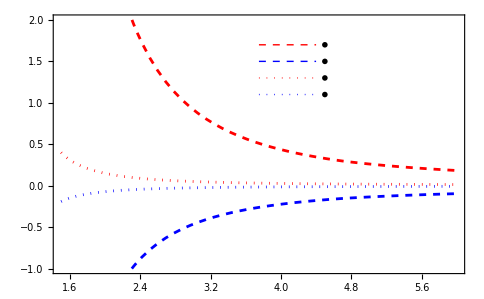

```mathematica
Plot[{
10^9 DwJ[0,μ,LPC,I,fπ,aπ],
10^9 DwJ[0,μ,LPC,II,fπ,aπ],
10^9 DwJ[0,μ,RQCD,I,fπ,aπ],
10^9 DwJ[0,μ,RQCD,II,fπ,aπ]
},{μ,mc,4mc},Frame->True,PlotRange->{{mc,6},{-1,2}},
FrameLabel->{MaTeX["\\mu (\\rm GeV)"],MaTeX["\\Gamma(T^{(0)}_{4c}\\to\\pi^+\\pi^-)(\\times10^{-9}{\\rm GeV})"]},
Epilog->{
{Red,Dashed,Line[{{3.75,1.7},{4.4,1.7}}]},Text[MaTeX["\\mbox{LPC Model-I}"],{4.5,1.7},{-1,0}],
{Blue,Dashed,Line[{{3.75,1.5},{4.4,1.5}}]},Text[MaTeX["\\mbox{LPC Model-II}"],{4.5,1.5},{-1,0}],
{Red,Dotted,Line[{{3.75,1.3},{4.4,1.3}}]},Text[MaTeX["\\mbox{RQCD Model-I}"],{4.5,1.3},{-1,0}],
{Blue,Dotted,Line[{{3.75,1.1},{4.4,1.1}}]},Text[MaTeX["\\mbox{RQCD Model-II}"],{4.5,1.1},{-1,0}]
},
PlotStyle->{{Red,Dashed},{Blue,Dashed},{Red,Dotted},{Blue,Dotted}}]
```

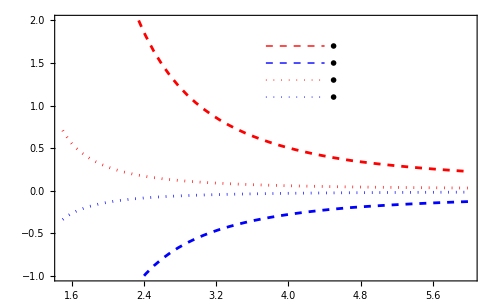

```mathematica
Plot[{
10^9 DwJ[0,μ,LPC,I,fK,aK],
10^9 DwJ[0,μ,LPC,II,fK,aK],
10^9 DwJ[0,μ,RQCD,I,fK,aK],
10^9 DwJ[0,μ,RQCD,II,fK,aK]
},{μ,mc,4mc},Frame->True,PlotRange->{{mc,6},{-1,2}},
FrameLabel->{MaTeX["\\mu (\\rm GeV)"],MaTeX["\\Gamma(T^{(0)}_{4c}\\to K^+K^-)(\\times10^{-9}{\\rm GeV})"]},
Epilog->{
{Red,Dashed,Line[{{3.75,1.7},{4.4,1.7}}]},Text[MaTeX["\\mbox{LPC Model-I}"],{4.5,1.7},{-1,0}],
{Blue,Dashed,Line[{{3.75,1.5},{4.4,1.5}}]},Text[MaTeX["\\mbox{LPC Model-II}"],{4.5,1.5},{-1,0}],
{Red,Dotted,Line[{{3.75,1.3},{4.4,1.3}}]},Text[MaTeX["\\mbox{RQCD Model-I}"],{4.5,1.3},{-1,0}],
{Blue,Dotted,Line[{{3.75,1.1},{4.4,1.1}}]},Text[MaTeX["\\mbox{RQCD Model-II}"],{4.5,1.1},{-1,0}]
},
PlotStyle->{{Red,Dashed},{Blue,Dashed},{Red,Dotted},{Blue,Dotted}}]
```

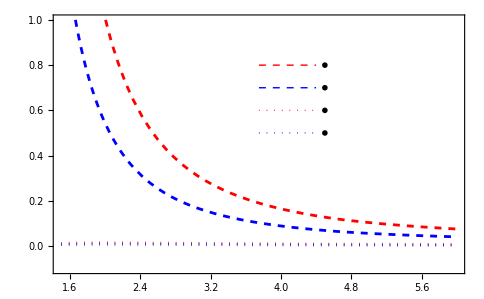

```mathematica
Plot[{
10^9 DwJ[2,μ,LPC,I,fπ,aπ],
10^9 DwJ[2,μ,LPC,II,fπ,aπ],
10^9 DwJ[2,μ,RQCD,I,fπ,aπ],
10^9 DwJ[2,μ,RQCD,II,fπ,aπ]
},{μ,mc,4mc},Frame->True,PlotRange->{{mc,6},{-0.1,1}},
FrameLabel->{MaTeX["\\mu (\\rm GeV)"],MaTeX["\\Gamma(T^{(2)}_{4c}\\to\\pi^+\\pi^-)(\\times10^{-9}{\\rm GeV})"]},
Epilog->{
{Red,Dashed,Line[{{3.75,0.8},{4.4,0.8}}]},Text[MaTeX["\\mbox{LPC Model-I}"],{4.5,0.8},{-1,0}],
{Blue,Dashed,Line[{{3.75,0.7},{4.4,0.7}}]},Text[MaTeX["\\mbox{LPC Model-II}"],{4.5,0.7},{-1,0}],
{Red,Dotted,Line[{{3.75,0.6},{4.4,0.6}}]},Text[MaTeX["\\mbox{RQCD Model-I}"],{4.5,0.6},{-1,0}],
{Blue,Dotted,Line[{{3.75,0.5},{4.4,0.5}}]},Text[MaTeX["\\mbox{RQCD Model-II}"],{4.5,0.5},{-1,0}]
},
PlotStyle->{{Red,Dashed},{Blue,Dashed},{Red,Dotted},{Blue,Dotted}}]
```

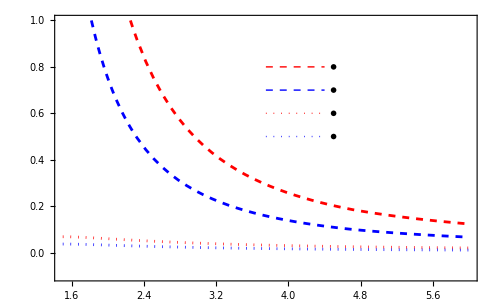

```mathematica
Plot[{
10^9 DwJ[2,μ,LPC,I,fK,aK],
10^9 DwJ[2,μ,LPC,II,fK,aK],
10^9 DwJ[2,μ,RQCD,I,fK,aK],
10^9 DwJ[2,μ,RQCD,II,fK,aK]
},{μ,mc,4mc},Frame->True,PlotRange->{{mc,6},{-0.1,1}},
FrameLabel->{MaTeX["\\mu (\\rm GeV)"],MaTeX["\\Gamma(T^{(2)}_{4c}\\to K^+K^-)(\\times10^{-9}{\\rm GeV})"]},
Epilog->{
{Red,Dashed,Line[{{3.75,0.8},{4.4,0.8}}]},Text[MaTeX["\\mbox{LPC Model-I}"],{4.5,0.8},{-1,0}],
{Blue,Dashed,Line[{{3.75,0.7},{4.4,0.7}}]},Text[MaTeX["\\mbox{LPC Model-II}"],{4.5,0.7},{-1,0}],
{Red,Dotted,Line[{{3.75,0.6},{4.4,0.6}}]},Text[MaTeX["\\mbox{RQCD Model-I}"],{4.5,0.6},{-1,0}],
{Blue,Dotted,Line[{{3.75,0.5},{4.4,0.5}}]},Text[MaTeX["\\mbox{RQCD Model-II}"],{4.5,0.5},{-1,0}]
},
PlotStyle->{{Red,Dashed},{Blue,Dashed},{Red,Dotted},{Blue,Dotted}}]
```

### Tables

```mathematica
N2[ex_]:=N[ex,2]
```

#### J=0

```mathematica
{DwJ[0,2mc,LPC,I,fπ,aπ],DwJ[0,2mc,LPC,II,fπ,aπ],DwJ[0,2mc,RQCD,I,fπ,aπ],DwJ[0,2mc,RQCD,II,fπ,aπ]};
Rationalize[%,0]//N2
Rationalize[%%/Γtot,0]//N2
```

{9.2×10^-10,-4.6×10^-10,5.1×10^-11,-2.5×10^-11}

{7.7×10^-9,-3.9×10^-9,4.2×10^-10,-2.1×10^-10}

```mathematica
{DwJ[0,2mc,LPC,I,fK,aK],DwJ[0,2mc,LPC,II,fK,aK],DwJ[0,2mc,RQCD,I,fK,aK],DwJ[0,2mc,RQCD,II,fK,aK]};
Rationalize[%,0]//N2
Rationalize[%%/Γtot,0]//N2
```

{1.×10^-9,-5.5×10^-10,1.×10^-10,-5.3×10^-11}

{8.4×10^-9,-4.6×10^-9,8.5×10^-10,-4.4×10^-10}

#### J=2

```mathematica
{DwJ[2,2mc,LPC,I,fπ,aπ],DwJ[2,2mc,LPC,II,fπ,aπ],DwJ[2,2mc,RQCD,I,fπ,aπ],DwJ[2,2mc,RQCD,II,fπ,aπ]};
Rationalize[%,0]//N2
Rationalize[%%/Γtot,0]//N2
```

{3.2×10^-10,1.7×10^-10,1.2×10^-11,6.6×10^-12}

{2.7×10^-9,1.5×10^-9,1.×10^-10,5.5×10^-11}

```mathematica
{DwJ[2,2mc,LPC,I,fK,aK],DwJ[2,2mc,LPC,II,fK,aK],DwJ[2,2mc,RQCD,I,fK,aK],DwJ[2,2mc,RQCD,II,fK,aK]};
Rationalize[%,0]//N2
Rationalize[%%/Γtot,0]//N2
```

{4.8×10^-10,2.6×10^-10,4.1×10^-11,2.2×10^-11}

{4.×10^-9,2.2×10^-9,3.4×10^-10,1.8×10^-10}

#### J=0/J=2 @ T_(4b)

```mathematica
{DwJ[0,2mb,LPC,I,fπ,aπ,mb,Rbc],DwJ[0,2mb,LPC,II,fπ,aπ,mb,Rbc],DwJ[0,2mb,RQCD,I,fπ,aπ,mb,Rbc],DwJ[0,2mb,RQCD,II,fπ,aπ,mb,Rbc]};
Rationalize[%,0]//N2
```

{1.7×10^-14,-9.2×10^-15,1.6×10^-15,-9.×10^-16}

```mathematica
{DwJ[0,2mb,LPC,I,fK,aK,mb,Rbc],DwJ[0,2mb,LPC,II,fK,aK,mb,Rbc],DwJ[0,2mb,RQCD,I,fK,aK,mb,Rbc],DwJ[0,2mb,RQCD,II,fK,aK,mb,Rbc]};
Rationalize[%,0]//N2
```

{2.3×10^-14,-1.3×10^-14,3.8×10^-15,-2.2×10^-15}

```mathematica
{DwJ[2,2mb,LPC,I,fπ,aπ,mb,Rbc],DwJ[2,2mb,LPC,II,fπ,aπ,mb,Rbc],DwJ[2,2mb,RQCD,I,fπ,aπ,mb,Rbc],DwJ[2,2mb,RQCD,II,fπ,aπ,mb,Rbc]};
Rationalize[%,0]//N2
```

{7.7×10^-15,4.1×10^-15,1.×10^-15,5.4×10^-16}

```mathematica
{DwJ[2,2mb,LPC,I,fK,aK,mb,Rbc],DwJ[2,2mb,LPC,II,fK,aK,mb,Rbc],DwJ[2,2mb,RQCD,I,fK,aK,mb,Rbc],DwJ[2,2mb,RQCD,II,fK,aK,mb,Rbc]};
Rationalize[%,0]//N2
```

{1.3×10^-14,7.1×10^-15,2.8×10^-15,1.5×10^-15}